```mathematica
m:=2.36
h:=1
n:=2000
d:=2
l:=1
"causal events" n
"causal relations" n^2

A=CSDeSitterDGlobalSlabFull[h,d,n];
ρ:=CSize[A] / CVolume[A]
Subscript[C, 1]=CausalMatrix[A];
(*
Subscript[T, 1]=TestTau[A,All,"Timelike"];
T=Subscript[T, 1]*Subscript[C, 1];
*)
V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
T2=N[2*ArcCosh[Exp[V/(4ρ)]]];
K=1/2 Subscript[C, 1].Inverse[IdentityMatrix[n]+m^2/(2ρ)Subscript[C, 1]];
(*
Subscript[C, 1]//MatrixForm
Subscript[T, 2] //MatrixForm
K //MatrixForm
*)
points:=Transpose[{Flatten[T2],Flatten[K]}];
```

2000 causal events

4000000 causal relations

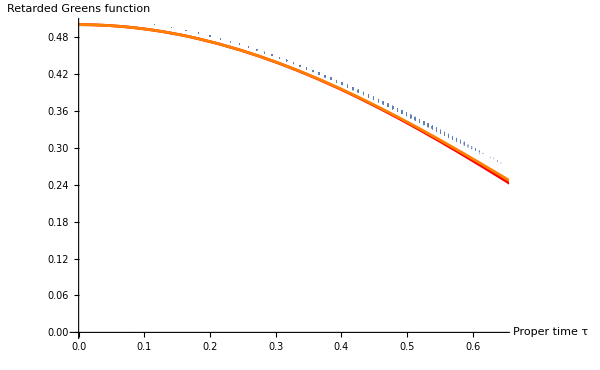

```mathematica
sample:=100000
Subscript[plot, 1]=ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Proper time τ","Retarded Greens function"}];
Subscript[plot, 2]=Plot[1/2 BesselJ[0,m*τ],{τ,0,h},PlotStyle->Red];
Subscript[plot, 3]=Plot[1/2 BesselJ[0,m*τ]+τ^2/24 BesselJ[2,m*τ],{τ,0,h},PlotStyle->Orange];
Show[Subscript[plot, 1],Subscript[plot, 2],Subscript[plot, 3]]
```

```mathematica
iΔ=N[I*(K-Transpose[K])];

{EE,VV}=Chop[Eigensystem[iΔ]];
Q = Transpose[VV] . DiagonalMatrix[Clip[N[EE],{0, Max[N[EE]]}]] . Conjugate[VV] // Chop;

points2=Transpose[{Flatten[T2],Flatten[Re[Q]]}];
```

```mathematica
sample=10000;
H1=(d-1)/2+Sqrt[((d-1)/2)^2-m^2 l^2]
H2=(d-1)/2-Sqrt[((d-1)/2)^2-m^2 l^2]

norm=Gamma[H1]*Gamma[H2]/((4*π)^(d/2)*l^2*Gamma[d/2])


plot1=ListPlot[points2,PlotStyle->PointSize[0.00001],ImageSize->600];

plot2=Plot[Re[norm*Hypergeometric2F1[H1,H2,d/2,1/2 *(1+Cosh[τ])]],{τ,0,2},PlotStyle->Red,AspectRatio->Automatic,AxesLabel->{"Proper time τ","Re[W]"}];
Show[plot1,plot2]
```

0.5+2.30643 ⅈ

0.5-2.30643 ⅈ

0.000356564+0. ⅈ

```mathematica
NIntegrate[1/Cos[x]^d,{x,-h,h}]
```

3.11482